# HW 7 - ASTR404 Created with Wolfram Mathematica 11.0 on October 14, 2016

## Daniel George - dgeorge5@illinois.edu

## Initialization

### Importing data for 15M star

```mathematica
data=SemanticImport[NotebookDirectory[]<>"15M_at_ZAMS.dat"];
(*Central density and radius of the star*)
ρc=10^data[Max,"logRho"];R=10^data[Max,"logR"];
```

### Solving the Lane-Emden equation

```mathematica
θ@n_:=θ@n=Module[{o=$MachineEpsilon ,x,y},
NDSolveValue[{x^-2D[x^2 D[y[x],x],x]+y[x]^n==0,y[o]==1,y'[o]==0,WhenEvent[Re@y[x]≤0,"StopIntegration"]},y,{x,o,10^2}]]
r@n_:=θ[n]⟦1,1,2⟧ (*Point where θ = 0*)
```

## Q1)

### Plotting density vs radius

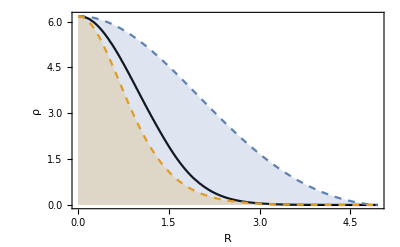

```mathematica
Show[ListLinePlot[data[10^#&,{"logR","logRho"}],PlotStyle->Black,PlotLegends->Placed[{"15M star"},{Right,Top}],Frame->True,FrameLabel->{"R","ρ"}],Plot[ρc(θ[#][r@# x/R])^#&/@{1.5,3}//Evaluate,{x,0,R},PlotLegends->Placed[{"n = 1.5","n = 3"},{Right,Top}],PlotStyle->Dashed,Filling->Bottom]]
```

## a)

The n = 3 polytrope is a good fit near the radius of the star (r > 3). Neither polytrope fits well in other regions.

## Q2)

### Gas and radiation pressure vs radius

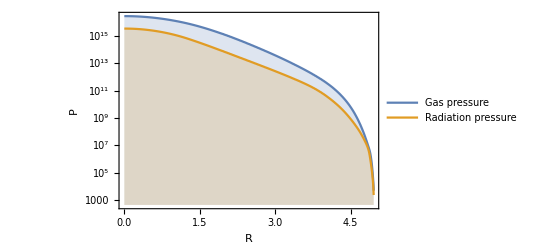

```mathematica
ListLogPlot[Transpose[{10^Normal@data[;;,"logR"],#}]&/@{10^Normal@data[;;,"logPgas"],10^Normal@data[;;,"logP"]-10^Normal@data[;;,"logPgas"]},PlotRange->All,Joined->True,Frame->True,Filling->Bottom,FrameLabel->{"R","P"},PlotLegends->Placed[{"Gas pressure","Radiation pressure"},{Left,Bottom}]]
```

## a)

The radiation pressure never dominates for this star. (The question does not ask why it doesn’t dominate, however this could be because the radiative temperature gradient assumption).

## b)

n ~ 1.5 corresponds to an ideal gas with low radiation whereas n ~ 3 corresponds to high radiation. However the star is closer to an n = 3 polytrope, despite the radiation pressure not dominating, because the Eddington model assumes a constant radiative temperature gradient.

## Q3)

### Energy generated in PP and CNO cycles

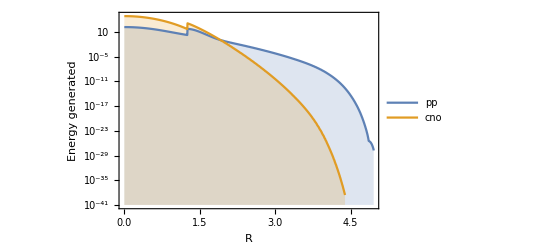

```mathematica
ListLogPlot[Transpose[{10^Normal@data[All,"logR"],Normal@data[All,#]}]&/@#,PlotRange->All,Filling->Bottom,Frame->True,FrameLabel->{"R","Energy generated"},PlotLegends->Placed[#,{Left,Bottom}],Joined->True]&@{"pp","cno"}
```

## a)

#### Point where total energy generation reduces by 50%

```mathematica
energy=Interpolation[Transpose@{10^Normal[data[All,"logR"]],Normal[Total/@data[All,{"cno","pp"}]]}];
FindRoot[energy@r==.5energy@energy⟦1,1,1⟧,{r,Sequence@@energy⟦1,1⟧}]
```

{r→0.408489}

The energy generation is primarily due to the CNO cycle in this region as seen in the figure above.

## Q4)

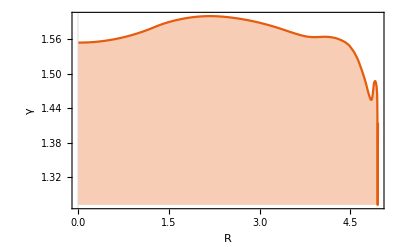

```mathematica
ListLinePlot[Transpose[{10^Normal@data[All,"logR"],Normal@data[All,#]}],PlotRange->All,PlotTheme->"Scientific",Filling->Bottom,Frame->True,PlotTheme->"Scientific",FrameLabel->{"R","γ"}]&@"gamma1"
```

## a)

The adiabatic index is always less than 5/3 for this star. 
This is means that the equation of state is relativistic (more radiation).

## Q5)

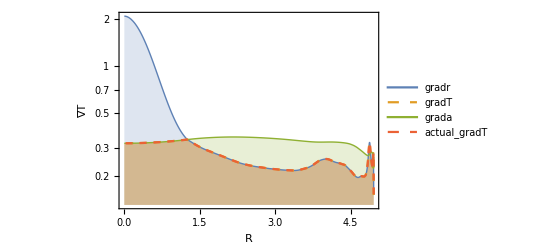

```mathematica
ListLogPlot[Transpose[{10^Normal@data[All,"logR"],Normal@data[All,#]}]&/@#,PlotRange->All,Filling->Bottom,PlotStyle->{Thick,Dashed},Frame->True,FrameLabel->{"R","∇T"},PlotLegends->Placed[#,{Right,Top}],Joined->True]&@{"gradr","gradT","grada","actual_gradT"}
```

## a)

Yes, for r less than about 1.1 the star is convective as can be seen from the plot above (grada ~ gradT). This is because the CNO cycle is dominant for this region (see Q3).

## Where are all these physicists??

-Graphics-